```mathematica
Clear["Global`*"]
```

### 基本閉路行列の関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
Pin=Table[{RandomReal[10],RandomReal[10]},{i,6}](*Point input*)
```

{{5.92374,3.92432},{2.69752,2.73217},{7.20109,7.6709},{3.2285,2.06453},{3.87776,4.70856},{1.51203,3.66943}}

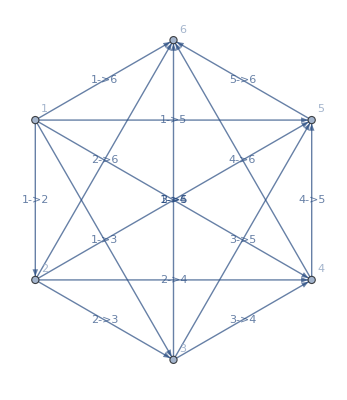

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"](*Ggraph input*)
```

```mathematica
h=LoopMatrix[Gin]
```

{{0,0,0,1,-1,0,0,0,0,0,0,0,0,0,1},{0,0,1,0,-1,0,0,0,0,0,0,0,0,1,0},{0,0,1,-1,0,0,0,0,0,0,0,0,1,0,0},{0,1,0,0,-1,0,0,0,0,0,0,1,0,0,0},{0,1,0,-1,0,0,0,0,0,0,1,0,0,0,0},{0,1,-1,0,0,0,0,0,0,1,0,0,0,0,0},{1,0,0,0,-1,0,0,0,1,0,0,0,0,0,0},{1,0,0,-1,0,0,0,1,0,0,0,0,0,0,0},{1,0,-1,0,0,0,1,0,0,0,0,0,0,0,0},{1,-1,0,0,0,1,0,0,0,0,0,0,0,0,0}}

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}](* Point Distance *)
```

{3.43944,3.95834,3.27462,2.19114,4.41907,6.6838,0.853039,2.30197,1.51124,6.87116,4.45197,6.95537,2.72258,2.34988,2.58388}

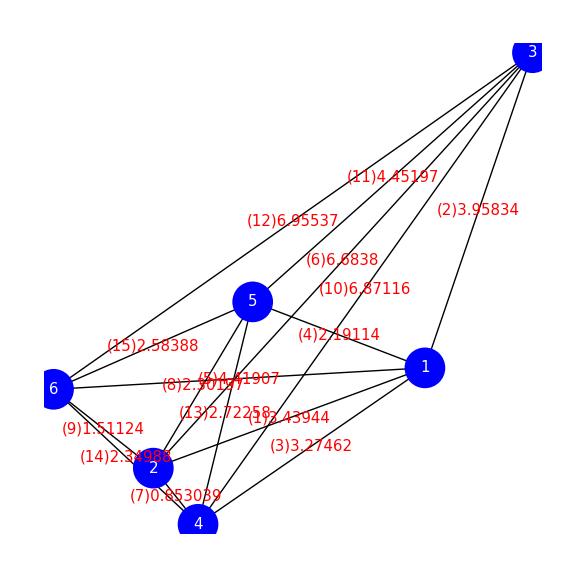

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[PD[[i]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}]
```

```mathematica
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD
```

{{3.43944,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,3.95834,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,3.27462,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.19114,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,4.41907,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,6.6838,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.853039,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.30197,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.51124,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,6.87116,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.45197,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.95537,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.72258,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.34988,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.58388}}

```mathematica
s=Table[0,{i,Length[EdgeRules[Gin]]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}](* Fundamental Loop Point *)
```

{{{1.51203,3.66943},{5.92374,3.92432},{3.87776,4.70856}},{{1.51203,3.66943},{5.92374,3.92432},{3.2285,2.06453}},{{3.87776,4.70856},{5.92374,3.92432},{3.2285,2.06453}},{{1.51203,3.66943},{5.92374,3.92432},{7.20109,7.6709}},{{3.87776,4.70856},{5.92374,3.92432},{7.20109,7.6709}},{{3.2285,2.06453},{5.92374,3.92432},{7.20109,7.6709}},{{1.51203,3.66943},{5.92374,3.92432},{2.69752,2.73217}},{{3.87776,4.70856},{5.92374,3.92432},{2.69752,2.73217}},{{3.2285,2.06453},{5.92374,3.92432},{2.69752,2.73217}},{{7.20109,7.6709},{5.92374,3.92432},{2.69752,2.73217}}}

```mathematica
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}](* 右回りならば負、左回りならば正 *)
```

{1,-1,-1,1,1,1,-1,-1,1,-1}

```mathematica
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}](* Fundamental Loop Area *)
```

{1.99067,3.75893,2.95941,8.10162,4.3336,3.86118,2.21854,2.48463,1.39348,5.28225}

```mathematica
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}](* 誘導起電力は右回りなら負、左回りなら正 *)
```

{1.99067,-3.75893,-2.95941,8.10162,4.3336,3.86118,-2.21854,-2.48463,1.39348,-5.28225}

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{-0.403368,0.847735,-0.732783,0.297274,-0.00885917,-0.0806824,0.446926,-0.193703,-0.575908,-0.27565,0.365983,0.676721,0.0336247,-0.595132,0.503178}

```mathematica
Reverse[Ordering[Abs[Curr]]]
```

{2,3,12,14,9,15,7,1,11,4,10,8,6,13,5}

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

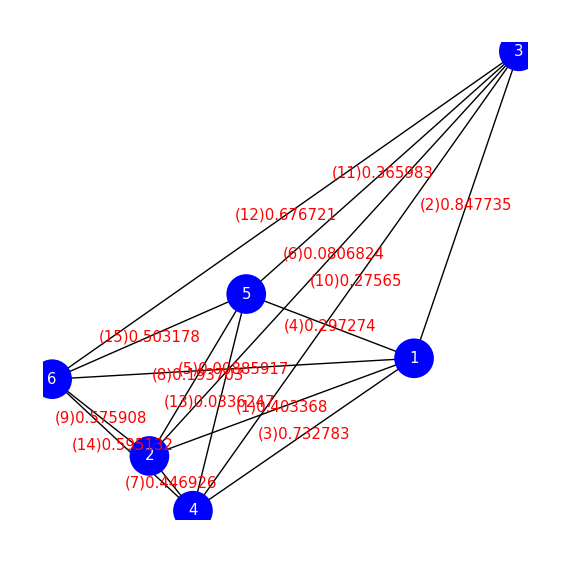

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
EdgeRules[Gin]
```

{1→2,1→3,1→4,1→5,1→6,2→3,2→4,2→5,2→6,3→4,3→5,3→6,4→5,4→6,5→6}

```mathematica
Reverse[Ordering[Abs[Curr]]]
```

{2,3,12,14,9,15,7,1,11,4,10,8,6,13,5}

```mathematica
MaxPartLoop={};
For[j=3,Length[MaxPartLoop]==0,j++,
MaxPartLoop=FindCycle[
Graph[EdgeList[Gout][[Reverse[Ordering[Abs[Curr]]][[Range[j]]]]]],
Infinity,All];
]
MaxPartLoop=EdgeRules[MaxPartLoop[[1]]]
```

{1→3,3→6,6→4,4→1}

```mathematica
RestVertex=Delete[VertexList[Gin],Table[{VertexList[MaxPartLoop][[i]]},{i,Length[VertexList[MaxPartLoop]]}]]
```

{3,4}

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiff[MaxPartLoop[[1]],RestVertex[[1]]]
```

3.35155

```mathematica
TriTourDiffList=Table[TriTourDiff[MaxPartLoop[[i]],RestVertex[[1]]],{i,Length[MaxPartLoop]}]
```

{3.35155,2.20427,0.92621,0.116673}

```mathematica
MinTriTourDiff=Min[Table[TriTourDiff[MaxPartLoop[[i]],RestVertex[[1]]],{i,Length[MaxPartLoop]}]]
```

0.116673

```mathematica
MinTriTourDiffPosition=FirstPosition[TriTourDiffList,MinTriTourDiff][[1]]
```

4

```mathematica
DelEdge=MaxPartLoop[[MinTriTourDiffPosition]]
```

1→6

```mathematica
VertexList[{DelEdge}]
```

{1,6}

```mathematica
InsertPartLoop=Append[Append[Delete[MaxPartLoop,MinTriTourDiffPosition],VertexList[{DelEdge}][[1]]->RestVertex[[1]]],RestVertex[[1]]->VertexList[{DelEdge}][[2]]]
```

{6→5,5→2,2→1,1→3,3→6}

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
TriTourDiffList[InsertPartLoop,RestVertex[[2]]]
```

{1.14169,2.21521,3.22989,3.01272,0.0967027}

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinTriTourDiffPosition[InsertPartLoop,RestVertex[[2]]]
```

5

```mathematica
DelEdge[PartLoop_,Vertex_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,Vertex]]]
```

```mathematica
DelEdge[InsertPartLoop,RestVertex[[2]]]
```

3→6

```mathematica
VertexInsertPartLoop[PartLoop_,Vertex_]:=(
Append[Append[Delete[PartLoop,MinTriTourDiffPosition[PartLoop,Vertex]],VertexList[{DelEdge[PartLoop,Vertex]}][[1]]->Vertex],Vertex->VertexList[{DelEdge[PartLoop,Vertex]}][[2]]]
)
```

```mathematica
VertexInsertPartLoop[InsertPartLoop,RestVertex[[2]]]
```

{6→5,5→2,2→1,1→3,3→4,4→6}